## WAVES and WHATNOT: Bessel Functions

## Raymond Yuan and Akshay Jaggi

Dr. Raulston and Dr Romero - Differential Equations 
ISP Presentation

## What is a Bessel Function?

The solution of a very particular differential equation that arises in a variety of physical situations.

That differential equation is conveniently named Bessel’s differential equation.

t^2 x''(t)+t x'(t)+(t^2-α^2)x(t)=0

```mathematica
x[t]/.DSolve[t^2*x''[t]+t*x'[t]+(t^2-α^2)x[t]==0,x[t],t][[1]]
```

BesselJ[α,t] C[1]+BesselY[α,t] C[2]

## Series Derivation of Besself Functions of the First Kind :3

Given the equation x^2 y''(x)+x y'(t)+(x^2-m^2)y(x)=0, m≥0, and the substitution of y as a power series: x^k∑_(n=0)^∞ a_n x^n, will provide the definition of the function in terms of the generating function.
y=∑_(n=0)^∞ a_n x^(n+k); 
y'=ka_0 x^(k-1)+∑_(n=1)^∞ a_n x^(n+k)=∑_(n=0)^∞ (n+k)a_n x^(n+k-1)
y''=∑_(n=0)^∞ (n+k)(n+k+1)a_n x^(n+k-2)
substitute
x^2 ∑_(n=0)^∞ (n+k)(n+k+1)a_n x^(n+k-2) + x  ∑_(n=0)^∞ (n+k)a_n x^(n+k-1) + x^2 ∑_(n=0)^∞ a_n x^(n+k)+m^2 ∑_(n=0)^∞ a_n x^(n+k)
==∑_(n=0)^∞ (n+k)(n+k+1)a_n x^(n+k)+ ∑_(n=0)^∞ (n+k)a_n x^(n+k)+∑_(n=0)^∞ a_n x^(n+k+2)+ ∑_(n=0)^∞ m^2 a_n x^(n+k)
==∑_(n=0)^∞ (n+k)(n+k+1)a_n x^(n+k)+ ∑_(n=0)^∞ (n+k)a_n x^(n+k)+∑_(n=2)^∞ a_(n-2)x^(n+k)+ ∑_(n=0)^∞ m^2 a_n x^(n+k)
get same index 
==(k)(k-1)a_0 x^k+(k+1)(k)a_1 x^(k+1)+ka_0 x^k+(k+1)a_1 x^(k+1)-m^2 a_0 x^k-m^2 a_1 x^(k+1)+∑_(n=2)^∞ [(n+k)(n+k-1)a_n+(n+k)a_n+a_(n-2)-m^2 a_n]x^(n+k)
simplify by coefficient
==a_0[k(k-1)+k-m^2]x^k+a_1[(k+1)k+(k+1)-m^2]x^(k+1)+∑_(n=2)^∞ [(n+k)(n+k-1)a_n+(n+k)a_n+a_(n-2)-m^2 a_n]x^(n+k)
in order for the bessel function to equal 0, our series approximation's coefficients must all equal to 0 as well (centered on 0).
therefore for n=0
	a_0(k^2-m^2)=0
n=1
	a_1(k^2+2k+1-m^2)=0
n≥ 2
	(n+k)(n+k-1)a_n+(n+k)a_n+a_(n-2)-m^2 a_n
Our Indicial equation (also known as the characteristic equation of the bessel function) is the recurrence equation taht we get from solving our ODE by setting n=0 and must be equal to  0 will thus be:
a_0(k^2-m^2)=0
since a_0≠ 0, k^2=m^2; or k=±m
substitute into our coefficient patterns
n=1
	a_1(k^2+2k+1-k^2)=0
	==a_1(2k+1)=0
This implies a_1= 0, given because k=m and that m≥ 0
n≥ 2
	(n+k)(n+k-1)a_n+(n+k)a_n+a_(n-2)-m^2 a_n
	==Simplify[(n+k)(n+k-1)a_n+(n+k)a_n+a_(n-2)-m^2 a_n==0]/.k→m
	==a_(-2+n)+(2 m n+n^2) a_n==0
therefore  our recurrence is as follows for n≥ 2
	a_n=(-a_(n-2))/(n^2+2m n)
However, knowing that a_1=0, indicates that every odd term will be equal to 0 because of the recurrence pattern and thus the recurrence relationship can be analyzed by only its even terms. Thus it is convenient to make the substitution n=2p

 a_(2p)=(-a_(2p-2))/((2p)^2+2m (2p)); a_(2p)=(-a_(2(p-1)))/(4p(p+m)); analyze coefficients
a_2=-a_0/(4(1+m))
a_4=-a_2/(4*2(2+m));
	==a_0/(4*4*2(1+m)(2+m))
a_6=-a_4/(4*3(3+m));
	==-a_0/(4*4*4*3*2*1(1+m)(2+m)(3+m))
Thus a solution of the bessel functions can be described as such:
y=∑_(p=0)^∞ [((-1)^p a_0)/(2^(2p)p!(1+m)(2+m)+...+(p+m))]x^(2p+m)
which is fairly disgusting... so using the extrodinarily clever substitution with the gamma function:
a_0=1/(2^m Γ(m+1)), you can simplify our equation quite nicely, knowing the basic property of gamma functions, that is xΓ(x)=Γ(x+1) , which also reveals that Γ(x+1)=x!
y=∑_(p=0)^∞ [(-1)^p/(p!(1+m)(2+m)+...+(p+m)Γ(m+1))]x^(2p+m)/2^(2p+m)
	y=∑_(p=0)^∞ [(-1)^p/(p!Γ(p+m+1))](x/2)^(2p+m)
when our constant m is equal to a n ,Γ(k+p+1)=(p+n)! Thus the bessel function of n^th order will be as shown
											J_n(x)=∑_(p=0)^∞ [(-1)^p/(p!(p+n)!)](x/2)^(2p+n)

```mathematica
bessel1[n_]:=∑_(p=0)^5 (-1)^p/(p!(p+n)!)(x/2)^(2p+n);
bessel1[0]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600

```mathematica
Series[BesselJ[0,x],{x,0,10}]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+O[x]^11

## Bessel Eigenvalues

The Bessel function differential equation can be linearized using the change of variables represented below.

Initial Equation:

```mathematica
Clear[p]
```

```mathematica
t^2*x''[t]+t*x'[t]+(t^2-p^2)x[t]==0
```

(-p^2+t^2) x[t]+t x'[t]+t^2 x''[t]==0

Set x’[t]=y[t] and x’’[t] = y’[t]. This first definition gives the function x’[t], which is very useful later on, so we’ll save it as the function f.

```mathematica
f=y[t]
```

y[t]

```mathematica
t^2*y'[t]+t*y[t]+(t^2-p^2)x[t]==0
```

(-p^2+t^2) x[t]+t y[t]+t^2 y'[t]==0

In order to obtain an equation for y’[t], we’ll use Solve.

```mathematica
g=y'[t]/.Solve[t^2*y'[t]+t*y[t]+(t^2-p^2)x[t]==0,y'[t]][[1]]
```

(p^2 x[t]-t^2 x[t]-t y[t])/t^2

Now, the equilibrium point of the f, g system can be found using a quick replace all.

```mathematica
Solve[{f==0,g==0}/.{x[t]->x,y[t]->y},{x,y}]
```

{{x→0,y→0}}

The coefficient matrix of the system can then be used to find the eigenvalues. In the case of the bessel function system, the eigenvalues are time depedent. This indicates that the function’s behavior near (0,0) varies over time.

```mathematica
co={{0,1},{(p^2-t^2)/t^2,-1/t}}
```

{{0,1},{(p^2-t^2)/t^2,-1/t}}

```mathematica
Eigenvalues[co]
```

{(-t-t √(1+4 p^2-4 t^2))/(2 t^2),(-t+t √(1+4 p^2-4 t^2))/(2 t^2)}

Here is a phase plane plot of x’ and y’ against each other.

```mathematica
Clear[p]
Manipulate[StreamPlot[{f,g}/.{x[t]->x,y[t]->y,t->d,p->0},{x,-5,5},{y,-5,5}, PlotLabel->Evaluate[Eigenvalues[co]/.{t->d,p->0}//N]],{d,10^-9,20}]
```

Interestingly, the Eigenvalues are a saddle node for t=0, a sink for 0<t<=0.5, a spiral sink for 0.5<t<=10. For t>10, the function begins behaving much like a center as the real component of the eigenvalues approach zero.

Let’s apply this to a specific solution with p=0 and the initial speed zero and position 1.

```mathematica
DSolve[{t^2*y'[t]+t*y[t]+(t^2-p^2)x[t]==0,y[t]==x'[t]},{x[t],y[t]},t]
```

{{x[t]→BesselJ[p,t] C[1]+BesselY[p,t] C[2],y[t]→1/2 (BesselJ[-1+p,t]-BesselJ[1+p,t]) C[1]+1/2 (BesselY[-1+p,t]-BesselY[1+p,t]) C[2]}}

Assuming p is zero...

```mathematica
{m,n}={x[t],y[t]}/.Quiet[DSolve[{t^2*y'[t]+t*y[t]+(t^2-p^2)x[t]==0,y[t]==x'[t],x[0]==.1,y[0]==0}/.p->0,{x[t],y[t]},t]][[1]]
```

{0.1 BesselJ[0,t],-0.1 BesselJ[1,t]}

Let’s take a look at both plots against time...

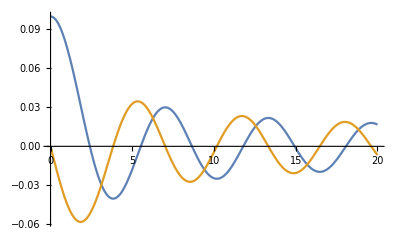

```mathematica
Plot[{m,n},{t,0,20}]
```

And here’s a phase plane plot of m and n.

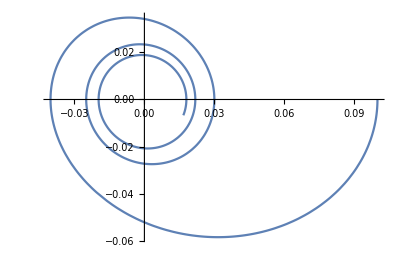

```mathematica
ParametricPlot[{m,n},{t,0,20}]
```

Here, we’ll vary the inital position. Then we can watch as the plot spirals toward the eq point at (0,0). The spiral becomes more circular over time. The most important outcome of the eigenvalue study is that the Bessel function behaves much like a traditional cosine function at large values of t. Sometimes, this code does no properly clear p, so you’ll need to evaluate just this cell a second time.

```mathematica
Clear[p]
Manipulate[Show[StreamPlot[{f,g}/.{x[t]->x,y[t]->y,t->d,p->0},{x,-5,5},{y,-5,5}],ParametricPlot[Evaluate[{x[t],y[t]}/.Quiet[DSolve[{x'[t]==f,y'[t]==g,x[0]==l,y[0]==0}/.{p->0},{x[t],y[t]},t]][[1]]],{t,0,d},PlotRange->{-10,40},PlotStyle->{Red,Thick}], PlotLabel->Evaluate[Eigenvalues[co]/.{t->d,p->0}//N]],{{l,3,"Initial Position"},-5,5},{{d,10^-9,"Time"},10^-9,30}]
```

Varying the initial condition leads to changing bessel function plots as seen below.

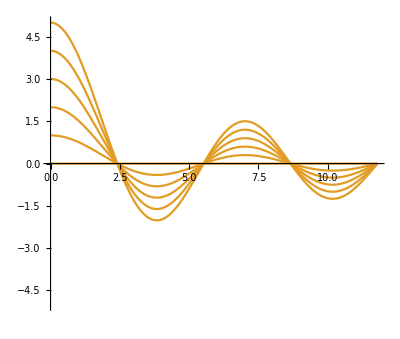

```mathematica
r[m1_]:=Evaluate[{x[t]}/.Quiet[DSolve[{x'[t]==f,y'[t]==g,x[0]==m1,y[0]==0}/.{p->0},{x[t],y[t]},t]][[1]]]
Show[Table[ParametricPlot[{t,r[m1]},{t,0,BesselJZero[0,4]}],{m1,0,5}],PlotRange->{-5,5}]
```

## Some Examples

```mathematica
-Graphics--Graphics-         -Graphics-;
```

## Linear Independence

Suppose we have two functions of t called u and v...

t^2 u''+t u' +(t^2-α^2)u=0
t^2 v''+t v' +(t^2-α^2)v=0

Simplify

t u''+u' +t u=0
t v''+v' +t v=0

Multiply by opposite function and subtract

v(t u''+u' +t u)-u(t v''+v' +t v)=0
t(v u''-u v'') + u'v-u v' =0
d/(d t)[t(u'v-u v')]=0

So t^2(u'v-u v') is a constant, which we’ll call B

(u'v-u v')/v^2=d/(d t)(u/v)=B/(t v^2)
u/v=A+B∫(d t)/(t v^2)
If v=J_m(t), then u = A J_m(t)+B J_m(t)∫(d t)/(t J_m^2(t))

We'll call J_m(t)∫(d t)/(t J_m^2(t))=Y_m(t)

v=J_m(t)
u=A J_m(t)+B Y_m(t)
		x(t)=v(t)+u(t)
        =J_m(t)+AJ_m(t)+B Y_m(t)
        =A' J_m(t) + B Y_m(t)

Thus the two final linearly independent solutions of the Bessel Equation are J_m(t) and Y_m(t)

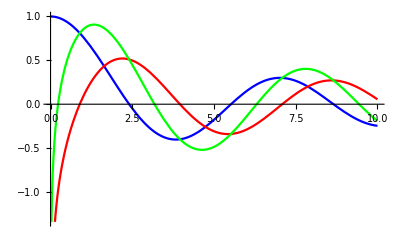

```mathematica
Plot[{BesselJ[0,x],BesselY[0,x],BesselJ[0,x]+BesselY[0,x]},{x,0,10},PlotStyle->{Blue, Red,Green}]
```

## A Simple Example: The Hanging Chain

For this example, we have a load of handwritten work solving for the final Bessel function solution. We can turn this in to you separately if you wish to see it. However, the animation itself is nice to look at. Here, a flexible uniform chain is oscillating under the influence of gravity. The top of the chain is held stationary while the rest of the chain is left free to move. The chain has a certain number fundamental nodes that depends on the frequency of oscillation. By changing the “order” of the frequency, we can see the number of nodes of the oscillating chain increase.

```mathematica
r=N[BesselJZero[0,{1,2,3,4}]]
ω=w/.Table[FindRoot[2*w*Sqrt[x/9.8]-r[[i]]/.{x->1},{w,1}],{i,1,4}]
Manipulate[Rotate[Plot[BesselJ[0,2ω[[k]]Sqrt[x/9.8]]*Cos[ω[[k]]*t],{x,0,1},PlotRange->{-1,1}],π/2],{{k,1,"Order"},{1,2,3,4}},{{t,0,"Time"},0,π}]
```

{2.40483,5.52008,8.65373,11.7915}

{3.76415,8.64029,13.5452,18.4567}

Mr. Friedman recommended looking at how various modes can be added to create unique chain behaviors. For instance, a chain of length L=2 can have its first three modes summed M_0+.5 M_1+.25 M_2 giving a behavior of a limp, dangling chain.  Lastly, we add a dampening factor to make it even more realistic. While the behavior isn’t entirely realistic, it seems a very good model of reality. Play the manipulate slowly for best viewing experience :3

```mathematica
ω2=w/.Table[FindRoot[2*w*Sqrt[x/9.8]-r[[i]]/.{x->2},{w,1}],{i,1,3}]
dangle[t_,x_]=BesselJ[0,2ω2[[1]]Sqrt[x/9.8]]*Cos[ω2[[1]]*t]+.5*BesselJ[0,2ω2[[2]]Sqrt[x/9.8]]*Cos[ω2[[2]]*t]+.25*BesselJ[0,2ω2[[3]]Sqrt[x/9.8]]*Cos[ω2[[3]]*t]
Manipulate[Rotate[Plot[dangle[t,x],{x,0,2},PlotRange->{-4,4}],π/2],{t,0,2π}]
Manipulate[Rotate[Plot[Exp[-.1*t]dangle[t,x],{x,0,2},PlotRange->{-4,4}],π/2],{t,0,5π}]
```

{2.66165,6.10961,9.57792}

BesselJ[0,1.70047 √x] Cos[2.66165 t]+0.5 BesselJ[0,3.90328 √x] Cos[6.10961 t]+0.25 BesselJ[0,6.11911 √x] Cos[9.57792 t]

## Hot Rod: Heat Equation Example

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

A cool disk is attached to a hot pipe to help cool the pipe. The equation describing the heating of one ring element is

-k A(r)   (d T)/(d r) (at r) =-k A(r)   (d T)/(d r)(at r+d r)+h A_c(r)(T-T_∞)   
		A(r)=2π r t            A_c(r) = 2(2π r d r)

Conduction is represented by Fourier’s law, where the first term is evaluated at r and the second is evaluated at r+dr. 
The first term represents the heat entering the ring element, and the second term represents the heat leaving the ring element. 
The final term is Newton’s Law of Cooling to represent heat loss due to convection. 
The LHS of the equation is the heat entering the ring element, which should be equal to the RHS aka the heat leaving the ring element. 
Substituting the A terms into the initial equation, we have

k ( 2π r t) (d T)/(d r)(at r+d r)-k (2π r t ) (d T)/(d r)(at r) -h  2(2π r d r)(T-T_∞) =0
r  (d T)/(d r)(at r+d r)-r(d T)/(d r)(at r) -(2r h d r)/(k t)(T-T_∞) =0
(r  (d T)/(d r)(at r+d r)-r(d T)/(d r)(at r))/(d r)-(2r h)/(k t)(T-T_∞) =0

The above expression is basically the difference quotient, so if we take the limit as dr -> 0, we get

d/(d r)(r(d T)/(d r))-(2r h)/(k t)(T-T_∞) =0

Multiply that out.

r^2(d^2 T)/(d r^2)+r(d T)/(d r)-(2h r^2)/(k t)(T-T_∞) =0

Make some substitutions: θ = T-T_∞ and ρ= ⅈ r √(2h/k t)

ρ^2(d^2 θ)/(d ρ^2)+ρ(d θ)/(d ρ)-ρ^2 θ=0

Thus the solution will be a zero order bessel function of r with conversion contstant ⅈ m = ⅈ √(2h/k t) and solution constants p and q determined by the initial conditions.

```mathematica
Clear[m,p,q,r]
th[r_]=p*BesselJ[0,ⅈ*m*r]+q*BesselY[0,ⅈ*m*r]
```

p BesselJ[0,ⅈ m r]+q BesselY[0,ⅈ m r]

```mathematica
{p,q}={p,q}/.Solve[{th[1]==100,th[5]==10},{p,q}][[1]]
```

{(10 (BesselY[0,ⅈ m]-10 BesselY[0,5 ⅈ m]))/(BesselJ[0,5 ⅈ m] BesselY[0,ⅈ m]-BesselJ[0,ⅈ m] BesselY[0,5 ⅈ m]),-(10 (BesselJ[0,ⅈ m]-10 BesselJ[0,5 ⅈ m]))/(BesselJ[0,5 ⅈ m] BesselY[0,ⅈ m]-BesselJ[0,ⅈ m] BesselY[0,5 ⅈ m])}

For different values of m, the heat will distribute itself differently throughout the cooling disk.

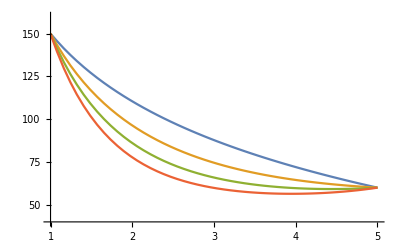

```mathematica
Plot[Evaluate[Table[(50+th[r])/.m->w,{w,{.1,.5,.75,1}}]],{r,1,5},PlotRange->{40,160}]
```

We’ll then plot the heat distribution for m=.75 on the disk within the radius r=5. The inner red ring is the hot cylinder at 150 temperature units. The outer black ring represents the edge of the cooling disk at 60 temperature units.

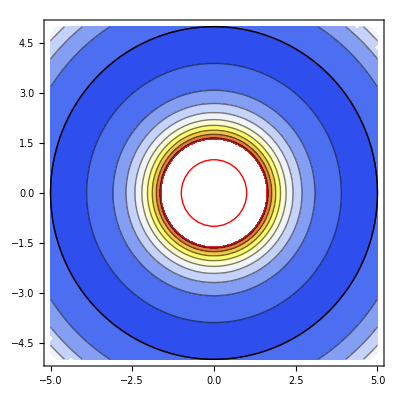

```mathematica
Show[ContourPlot[ (50+th[r])/.{m->.75,r->Sqrt[x^2+y^2]},{x,-5,5},{y,-5,5},ColorFunction->"TemperatureMap"],Graphics[{Thick,Circle[{0,0},5],Red,Thick,Circle[{0,0},1]}]]
```

## Fluid Applications

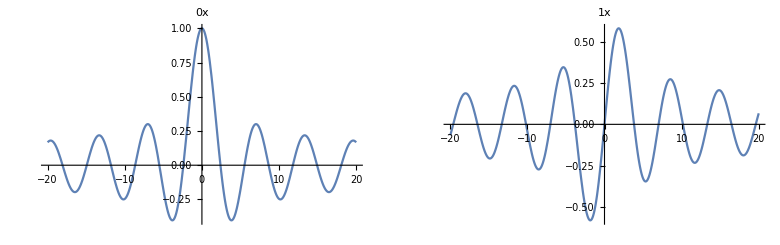

```mathematica
GraphicsRow[{Plot[BesselJ[0,x],{x,-20,20},PlotLabel->BesselJ[0,x],ImageSize->Medium],Plot[BesselJ[1,x],{x,-20,20},PlotLabel->BesselJ[1,x],ImageSize->Medium]}]
```

```mathematica
Sort[DeleteDuplicates[x/.Table[FindRoot[BesselJ[0,x],{x,i}],{i,1,10}]]]
```

{-52.6241,2.40483,5.52008,5.52008,8.65373}

```mathematica
Sort[DeleteDuplicates[x/.Table[FindRoot[BesselJ[1,x],{x,i}],{i,1,10}]]]
```

{1.32349×10^-20,3.83171,3.83171,3.83171,7.01559,7.01559,7.01559,10.1735,10.1735}

```mathematica
Quiet[Sort[DeleteDuplicates[x/.Table[FindRoot[BesselJ[1.5,x],{x,i}],{i,1,10}]]]]
```

{-29.8116+0. ⅈ,-7.80224×10^-6+0. ⅈ,0.0000110438,4.49341,7.72525,10.9041}

```mathematica
Sort[DeleteDuplicates[x/.Table[FindRoot[BesselJ[2,x],{x,i}],{i,1,10}]]]
```

{-30.5692,6.1926×10^-9,6.60233×10^-9,5.13562,5.13562,5.13562,8.41724,8.41724,11.6198,43.1535}

```mathematica
Sort[DeleteDuplicates[x/.Table[FindRoot[BesselJ[3,x],{x,i}],{i,1,12}]]]
```

{-154.695,-6.38016,1.40495×10^-8,1.71918×10^-8,2.01405×10^-8,6.38016,6.38016,6.38016,9.76102,9.76102,9.76102,13.0152}

```mathematica
cool0={2.404825557695773,5.520078110286309,8.65372791291}
cool1={3.83171,7.01558666981561,10.173468135062722}
cool15={4.493409457909064,7.725251836937707,10.904121659428899}
cool2={5.13562230184068,8.41724414039983,11.619841172149059}
cool3={6.380161895923981,9.76102312998153,13.015200721698434}
```

{2.40483,5.52008,8.65373}

{3.83171,7.01559,10.1735}

{4.49341,7.72525,10.9041}

{5.13562,8.41724,11.6198}

{6.38016,9.76102,13.0152}

```mathematica
Zeros[z]=BesselJ[3,z]
```

BesselJ[3,z]

Solutions of the Bessel equation of order zero and order one (J0(x))can be seen as above. One can find the radial modes of vibration of such a drum by seeting x=ru, and thus the modes of vibrations would have the form J0(ur). r=1, at the rim, and j0(u)=0 initially, when it is still. Thus the zeroes of J0(x) give the frequencies of radial vibrations of a circular drum. The first two fundamental frequencies will be 2.404 and 5.52

Notice that the Mode given as (d,c) where d is number of nodal diameters c is the number of nodal circles can be seen to be d=nth order of Bessel function and c to be the root of that order bessel function

The smallest associated frequency of vibration is the smallest zero of the J0 bessel function so it can be described as Bessel[0,2.4*r]*Cos[2.4t] for the first one 
Given initial conditions of r0=1 and t0=2Pi
Mode(0,1)

```mathematica
Clear[w,r]
Manipulate[Module[{fj},fj[r_,x_]:=If[w==0,BesselJ[w,v*r]*Cos[2Pi*t]/1.5,BesselJ[w,v*r]*Sin[w*x]Sin[2Pi*t]];{GraphicsRow[{Show[ParametricPlot3D[{1.5r*Cos[x],1.5r*Sin[x],fj[r,x]},{x,0,2Pi},{r,0,1},PlotRange->{-1.5,1.5},ImageSize->Medium,PlotStyle->Directive[Orange,Specularity[White,40]],Mesh->None,PlotPoints->25,ViewPoint->Right],Graphics3D[{Blue,Opacity[.2],Cylinder[{{0,0,0},{0,0,-1}},1.5]}]],
Show[ParametricPlot3D[{1.5r*Cos[x],1.5r*Sin[x],fj[r,x]},{x,0,2Pi},{r,0,1},PlotRange->{-1.5,1.5},ImageSize->Medium,PlotStyle->Directive[Orange,Specularity[White,40]],Mesh->None,PlotPoints->25],Graphics3D[{Blue,Opacity[.2],Cylinder[{{0,0,0},{0,0,-1}},1.5]}]],Plot[Evaluate[fj[r,k]],{r,-1,1},PlotRange->{-1,1},ImageSize->Medium]}]}],{t,(Pi/2)/2.4048,5},{{k,0,"Cross Section"},0,π},{{w,0,"Order"},{0,1,1.5,2,3}},{{v,cool0[[1]],"Zeros"},Which[w==0,cool0,w==1,cool1,w==1.5,cool15,w==2,cool2,w==3,cool3],ControlType->Setter}]
```

The Cross section manipulate will allow you to rotate the displayed cross section.